# Gravitational Memory Workbook

## Simon Thill, 2025

Code used while writing astrophysics senior thesis at Haverford College entitled “The Effect of Gravitational Memory on CMB Light.”

## Defining Variables and Functions

```mathematica
ClearAll["Global`*"]
```

### Rotation matrices and GW polarization tensors for a GW traveling along the z-axis.

```mathematica
Rz[ϕ_] := {{Cos[ϕ], -Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0},{0,0,1}} (*z-axis rotation*)
```

```mathematica
P = {{1,0,0},{0,-1,0}, {0,0,0}}; (*+ polarized wave*)
G = {{p,x,0},{x,-p,0}, {0,0,0}}; (*general wave polarization*)
X = {{0,1,0},{1,0,0}, {0,0,0}}; (*cross polarized wave*)
```

Applying the rotation matrix to + polarization. Tensors rotate as T’ = RTR^-1
To get the new tensor you apply the rotation matrix R and its inverse R^-1

```mathematica
Simplify[Rz[ϕ].P.Transpose[Rz[ϕ]]] //MatrixForm
```

(Cos[2 ϕ] | Sin[2 ϕ] | 0
Sin[2 ϕ] | -Cos[2 ϕ] | 0
0 | 0 | 0)

Rotations about the y and z-axes

```mathematica
Ry[α_] := {{Cos[α],0, Sin[α]}, {0,1,0},{-Sin[α], 0, Cos[α]}} (*y-axis rotation*)
Rx[α_] := {{1,0,0},{0, Cos[α], -Sin[α]}, {0,Sin[α],  Cos[α]}} (*x-axis rotation*)
```

### Variables and Functions

Constants: 
c=1, 
dG  Earth to GW source distance, 
tP time photon is received on Earth, 
tG time GW is received on Earth which we set to 0, 
(ϕ,θ) location on Earth’s sky where the photon is received
h0 GW strain amplitude measured on Earth
t time as measured on Earth 

Functions:
Functions are capitalized. A is the function that gives α for given parameters, RP is the function that gives rP.  
rP is the distance from GW source to photon
α is the angle between GW source and photon (measured up from GW propegation vector)
β is the azimuthal angle from the GW source to the photon 
dP is the distance from Earth to the photon
tmin is the initial time the photon encounters the GW
n is the vector pointing to point on the sky where the photon is found

```mathematica
$Assumptions=dG>0&&h0>0&&tP>tG&&0<=θ<=2 π&&t∈Reals;
c= 1;
tG = 0;
M[dP_, dG_] := If[dP>dG,ArcCos[dG/dP],0];
(*A[dP_, dG_, θ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] *)
DP[tP_, t_] := c(tP-t)
(*DP[tP_, t_] := If[tP>t,c(tP-t), 0]*) (*solves for if tP > t, but shouldn't be needed, although it did change the ϵ and h expresions a little*) 
Tmin[tG_, tP_, dG_,θ_] := (-c tG^2+2 dG tG +c tP^2 - 2 dG tP Cos[θ])/(-2 c tG + 2 dG + 2 c tP - 2 dG Cos[θ])
RP[dG_,tP_, t_,θ_] := Sqrt[dG^2+(tP-t)^2-2 dG(tP-t)Cos[θ] ]
n[θ_] := {Sin[θ], 0, Cos[θ]} (*2D looking vectore in x/z plane*)
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D looking vector *)
```

Functions for α and β, which are related to polar angles in the GW source’s coordinate system. These are the angles we rotate through to relate the polarization metric seen at Earth to the polarization metric seen by a photon at a given time.

```mathematica
A[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ]Cos[ϕ])/(dG - dP Cos[θ])]-π]] 
B[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ]Sin[ϕ])/(dG - dP Cos[θ])]-π]]
```

The trig expressions  Sin[2 ArcTan[x]] , Cos[2 ArcTan[x]], and  Cos[4 ArcTan[x]] appears frequently in our code. Here, we define functions which can be used to simplify these expressions automatically.

```mathematica
SinSimp[opp_, adj_] := FullSimplify[2*opp/Sqrt[adj^2+opp^2]*adj/Sqrt[adj^2+opp^2]] (*Simplifies Sin[2ArcTan[opp/adj]]*)(*Sin(2x) = 2CosxSinx*)
CosSimp[opp_, adj_] := FullSimplify[(adj/Sqrt[adj^2+opp^2])^2-(opp/Sqrt[adj^2+opp^2])^2] (*Simplifies Cos[2ArcTan[opp/adj]]*)(*Cos(2x) = Cos^2(x) - Sin^2(x)*)
CosSimp4AT[opp_, adj_] := 8 (adj/Sqrt[adj^2+opp^2])^4-8 (adj/Sqrt[adj^2+opp^2])^2+1 (*Cos[4x] = 8 Cos[x]^2-8 Cos[x]^2+1)*)
```

#### Testing functions

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t] , dG, θ, ϕ],{θ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", t = ",NumberForm[t,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{t,-10,-0.1},{ϕ,0,2π}] (*Plot of the angle α. This contains If statments so it's important to make sure the final plot is continuous.*)
```

```mathematica
Manipulate[Labeled[PolarPlot[tP - Tmin[tG, tP, dG,θ] ,{θ,0, 2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,4}] (*This is a polar plot of the total amout of time a photon has spent in the perturbed metric as a function of the distance to the GW and the time the photon in recived on Earth. The time the GW passed is t=0 and the GW source is along the z-axis (θ=0).*)
```

## Isotropic, Plus Polarized Metric in 2D Simplification

### GW Metric

Simplifying to 2D. Here, ϕ = β = 0 and we only need to consider α. We also consider an isotropic GW.

```mathematica
P // MatrixForm (*plus-polarized GW polarization metric*)
```

(1 | 0 | 0
0 | -1 | 0
0 | 0 | 0)

```mathematica
Ε[α_] := Ry[-α].P.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α.*)
Ε[α] //MatrixForm
```

(Cos[α]^2 | 0 | Cos[α] Sin[α]
0 | -1 | 0
Cos[α] Sin[α] | 0 | Sin[α]^2)

```mathematica
ϵ = FullSimplify[Ε[A[DP[tP,t], dG, θ,0]]]; (*plugging in α*)
MatrixForm[ϵ]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | 1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]
0 | -1 | 0
1/2 Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]] | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
ϵ = ({{(dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), 0, 1/2 SinSimp[(-t+tP) Sin[θ],dG+(t-tP) Cos[θ]]}, {0, -1, 0}, {1/2 SinSimp[(-t+tP) Sin[θ],dG+(t-tP) Cos[θ]], 0, ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])}}); (*applying trig simplifications*)
MatrixForm[ϵ]
```

((dG+(t-tP) Cos[θ])^2/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
0 | -1 | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) | 0 | ((t-tP)^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))

```mathematica
h2DIso= FullSimplify[1/RP[dG,tP, t,θ] ϵ ];(*full expression for Subscript[h, ij], without multiplying by initial amplitude h0*dG*)
MatrixForm[h2DIso]
```

((dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | -((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
0 | -1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0
-((t-tP) (dG+(t-tP) Cos[θ]) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | 0 | ((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

### Redshift

```mathematica
n[θ] (*2D looking vectore in x/z plane*)
```

{Sin[θ],0,Cos[θ]}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].h2DIso]] (*applying n^i n^j*)
```

(dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
HSimp[t_] := (dG^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)); (*n^i n^j Subscript[h, ij] as a function of time*)
```

```mathematica
ζSimp = FullSimplify[HSimp[Tmin[tG, tP, dG,θ]]] (*proportial to final redshfit*)
```

(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
ndotR = FullSimplify[Cos[π - θ - A[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,0]]] (*dot product of n and R when the photon first encounters the GW*)
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+ndotR] ζSimp ] (*full redshift equation*)
```

-(4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+ndotR] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
zSimp[θ_, dG_, tP_] := -((4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3))
```

```mathematica
(*Redshift function*)
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]  (*Plot of redshift*)
```

### Cross-Polarized GW Redshift

#### GW Metric

```mathematica
X // MatrixForm
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 0)

```mathematica
Εx[α_] := Ry[-α].X.Transpose[Ry[-α]] (*Polarization of a + GW at an angle α.*)
Εx[α] //MatrixForm
```

(0 | Cos[α] | 0
Cos[α] | 0 | Sin[α]
0 | Sin[α] | 0)

```mathematica
ϵx = FullSimplify[Εx[A[DP[tP,t], dG, θ,0]]]; (*plugging in α*)
MatrixForm[ϵx]
```

(0 | Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0
Piecewise[{{-1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {1/(√(1+((t-tP)^2 Sin[θ]^2)/(dG+(t-tP) Cos[θ])^2)), True}}] | 0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]-π]]]
0 | Sin[If[θ≤If[tP>dG+t,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[0])/(dG-(-t+tP) Cos[θ])]-π]]] | 0)

```mathematica
hxSimp= FullSimplify[1/RP[dG,tP, t,θ] ϵx ];(*full expression for Subscript[h, ij], without multiplying by initial amplitude h0*dG*)
MatrixForm[hxSimp]
```

(0 | Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0
Piecewise[{{-Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Abs[dG+(t-tP) Cos[θ]]/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]), True}}] | 0 | Piecewise[{{((-t+tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {((t-tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}]
0 | Piecewise[{{((-t+tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), (dG+t≥tP&&θ>0)||(dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]≤2 π)}, {((t-tP) Sin[θ])/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sign[dG+(t-tP) Cos[θ]]), True}}] | 0)

#### Redshift

```mathematica
n[θ] (*2D looking vectore in x/z plane*)
```

{Sin[θ],0,Cos[θ]}

```mathematica
FullSimplify[n[θ].Transpose[n[θ].hxSimp]] (*applying n^i n^j*)
```

0

There is no redshift due to a cross polarized wave in the x/z plane of our geometry. This is because when a  GW stretches and compresses spacetime there are four nodes which are not affected. For a cross-polarized wave (traveling along the z-axis), all points in the x/z plane are not affected. There will be a redshift effect in 3D

### Testing redshift results

Polarization component behavior.

```mathematica
FullSimplify[n[θ].Transpose[n[θ].ϵ]]
```

(dG^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])

```mathematica
ϵ2D[t_] := (dG^2 Sin[θ]^2)/(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])
```

```mathematica
FullSimplify[ϵ2D[Tmin[tG, tP, dG,θ]]]
```

(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2)

```mathematica
Manipulate[Labeled[Plot[(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2),{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]
```

```mathematica
Limit[(4 dG^2 (dG+tP-dG Cos[θ])^2 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^2),tP->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

One on R behavior

```mathematica
Manipulate[Labeled[Plot[1/RP[dG,tP, Tmin[tG, tP, dG,θ],θ] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,400}]
```

```mathematica
Limit[1/RP[dG,tP, Tmin[tG, tP, dG,θ],θ],tP->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

## Isotropic, Plus Polarized Metric in 2D binary’s plane: Work in Progress

ϕ = π/2
α = 0

```mathematica
A[DP[tP,t], dG, θ,ϕ]
```

If[θ≤If[-t+tP>dG,ArcCos[dG/(-t+tP)],0],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])]+π,If[θ≤2 π-M[-t+tP,dG],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])],ArcTan[((-t+tP) Sin[θ] Cos[ϕ])/(dG-(-t+tP) Cos[θ])]-π]]

```mathematica
Simplify[A[DP[tP,t], dG, θ,π/2]]
```

Piecewise[{{-π, dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {π, (dG+t≥tP&&θ≤0)||(dG+t<tP&&θ≤ArcCos[dG/(-t+tP)])}, {0, True}}]

```mathematica
Manipulate[Labeled[Plot[A[DP[tP, t] , dG, θ, π/2],{θ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", t = ",NumberForm[t,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,50},{tP,0.1,10},{t,-10,-0.1},{ϕ,0,2π}]
```

check this

```mathematica
Clear[HyzIso]
```

```mathematica
hyzIso = Simplify[Rx[B[DP[tP,t], dG, θ,π/2]].Ry[-A[DP[tP,t], dG, θ,π/2]].(P/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,π/2]]].Transpose[Rx[B[DP[tP,t], dG, θ,π/2]]]];
MatrixForm[hyzIso]
```

(1/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | 0 | 0
0 | -(dG+(t-tP) Cos[θ])^2/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)) | Piecewise[{{Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {-Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), True}}]
0 | Piecewise[{{Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), dG+t<tP&&θ>ArcCos[dG/(-t+tP)]&&θ+ArcCos[dG/(-t+tP)]>2 π}, {-Sin[2 ArcTan[((-t+tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), True}}] | -((t-tP)^2 Sin[θ]^2)/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2)))

```mathematica
Simplify[v[θ, π/2].Transpose[v[θ,π/2].hyzIso]]
```

-(Sin[θ] (dG^2 Sin[θ]-2 dG tP Cos[θ] Sin[θ]+2 t^2 Cos[θ]^2 Sin[θ]-4 t tP Cos[θ]^2 Sin[θ]+2 tP^2 Cos[θ]^2 Sin[θ]+dG t Sin[2 θ]-Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))

```mathematica
Hyz[t_] := -(Sin[θ] (dG^2 Sin[θ]-2 dG tP Cos[θ] Sin[θ]+2 t^2 Cos[θ]^2 Sin[θ]-4 t tP Cos[θ]^2 Sin[θ]+2 tP^2 Cos[θ]^2 Sin[θ]+dG t Sin[2 θ]-Cos[θ] (dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) Sin[2 ArcTan[((t-tP) Sin[θ])/(dG+(t-tP) Cos[θ])]]))/((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])^(3/2))
```

```mathematica
ζyz = FullSimplify[Hyz[Tmin[tG, tP, dG,θ]]]
```

-(8 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] (*angle between n and R*)
```

```mathematica
vdotRyz = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,π/2]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+vdotRyz] ζyz ] (*full redshift equation*)
```

(4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)

```mathematica
ZyzSimp[θ_, dG_, tP_] := (4 dG^2 (dG+tP-dG Cos[θ])^3 Sin[θ]^2)/(Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])] (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ])^3)
```

```mathematica
Manipulate[Labeled[Plot[ZyzSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,20},{tP,0.01,20}]  (*Plot of redshift*)
```

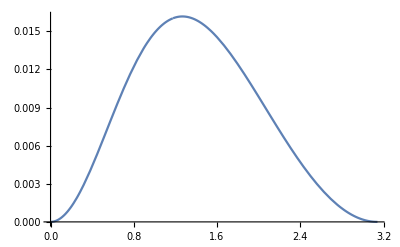

```mathematica
Plot[ZyzSimp[θ, 1, 4],{θ,0,π}]
```

## 3D, Isotropic, Plus-Polarised Wave: Work in Progress

```mathematica
h3DIso = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].(P/RP[dG,tP, t,θ]).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[h3DIso]
```

((dG+(t-tP) Cos[θ])^2/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))
Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | -((dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) | -((t-tP)^2 Sin[θ]^2 ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Applying Trig Simplifications

```mathematica
h3DIso =
```

### Considering If statements

### Redshift (haven’t applied trig simplifications yet)

```mathematica
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D looking vector *)
```

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ,ϕ].h3DIso]] (*not run on the simplified version*)
```

Cos[θ] Cos[ϕ] (Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]+Cos[ϕ] (Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]^2 Sin[ϕ]+Cos[ϕ] Sin[θ] (Cos[θ] (Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}])+((dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ] Sin[ϕ])+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Cos[θ] Sin[θ] (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))

```mathematica
H3DIso[t_] := Cos[θ] Cos[ϕ] (Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]+Cos[ϕ] (Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ]^2 Sin[ϕ]+Cos[ϕ] Sin[θ] (Cos[θ] (Piecewise[{{-Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]/(2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}])+((dG+(t-tP) Cos[θ])^2 Cos[ϕ] Sin[θ])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{-((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(2 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]) Sin[θ] Sin[ϕ])+(Sin[θ]^2 Sin[ϕ]^2 (-(dG+(t-tP) Cos[θ])^2+((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Cos[θ] Sin[θ] (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+2 (t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(√(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))
```

```mathematica
ζ3DIso = Simplify[H3DIso[Tmin[tG, tP, dG,θ]]]
```

Sin[θ] (Cos[θ] Cos[ϕ] (Piecewise[{{(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), True}}])+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ]+Cos[ϕ] (Cos[θ] (Piecewise[{{(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 (dG+tP-dG Cos[θ])^3 Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(2 tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(2 Cos[θ] (dG+tP-dG Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Sin[θ] Sin[ϕ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)))

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]] (*angle between n and R*)
```

```mathematica
vdotR3D = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,ϕ]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
FullSimplify[-1/2 1/Abs[1+vdotR3D] ζ3DIso ] (*full redshift equation*)
```

```mathematica
z3DIso[θ_,ϕ_, dG_, tP_] := -((Sin[θ] (Cos[θ] Cos[ϕ] (Piecewise[{{(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), True}}])+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ]+Cos[ϕ] (Cos[θ] (Piecewise[{{(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-(Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), True}}])+(2 (dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ] Sin[θ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))+(Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Sin[θ] Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Cos[ϕ] Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ] Sin[ϕ])+(8 (dG+tP-dG Cos[θ])^3 Sin[θ] Sin[ϕ]^2 (-(dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(2 tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ] (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(2 Cos[θ] (dG+tP-dG Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+2 tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ] Sin[2 ArcTan[(tP (2 dG+tP) Sin[θ] Sin[ϕ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))
```

### Plotting

```mathematica
Manipulate[Labeled[Plot[z3DIso[θ, ϕ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}]
```

```mathematica
Manipulate[Labeled[SphericalPlot3D[z3DIso[θ, ϕ, dG, tP] ,{θ,0, π},{ϕ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],}],Top],{dG,0.1,30},{tP,0.01,40}]
```

Max::nord: Invalid comparison with 6.05879-0.608876 ⅈ attempted.

Max::nord: Invalid comparison with 0.2244-0.608876 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord2: Comparison of Max[-6.05879+0.608876 ⅈ,-0.2244+0.608876 ⅈ,0.125072] and ∞ is invalid.

Min::nord2: Comparison of Max[-6.05879+0.608876 ⅈ,-0.2244+0.608876 ⅈ,0.000401443] and ∞ is invalid.

Min::nord2: Comparison of Max[0.0205472,6.05879-0.608876 ⅈ] and ∞ is invalid.

General::stop: Further output of Min::nord2 will be suppressed during this calculation.

## 3D, Anisotropic, Plus-Polarised Wave: Work in Progress

The plus polarized metric, P, is multiplied by a 0.5(1+Cos[α]^2) (anisotropic) and a 1/R (distance) scaling factor. It is then rotated about the y-axis through an angle -α and then rotated about the x-axis through an angle β. This gives the metric seen by a photon at a given time. 
Work in progress: We will be updating the anisotropic scaling factor.

```mathematica
h3DAniso = Simplify[Rx[B[DP[tP,t], dG, θ,ϕ]].Ry[-A[DP[tP,t], dG, θ,ϕ]].((P(1+Cos[A[DP[tP,t], dG, θ,ϕ]]^2))/(2*RP[dG,tP, t,θ])).Transpose[Ry[-A[DP[tP,t], dG, θ,ϕ]]].Transpose[Rx[B[DP[tP,t], dG, θ,ϕ]]]];
MatrixForm[h3DAniso]
```

(((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2) | Piecewise[{{-(((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | Piecewise[{{-(((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]
Piecewise[{{-(((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[θ] Sin[ϕ] Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((-17+Cos[4 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))
Piecewise[{{-(((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+Cos[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}] | ((-17+Cos[4 ArcTan[((-t+tP) Cos[ϕ] Sin[θ])/(dG+(t-tP) Cos[θ])]]) Sin[2 ArcTan[((-t+tP) Sin[θ] Sin[ϕ])/(dG+(t-tP) Cos[θ])]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])) | -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Applying Trig Simplifications

```mathematica
h3DAniso =Simplify[ ({{((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2), Piecewise[{{-(((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], Piecewise[{{-(((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ],dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}]}, {Piecewise[{{-(((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((t-tP) (3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) Sin[θ] Sin[ϕ] SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 (dG+(t-tP) Cos[θ]) √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)), ((-17+CosSimp4AT[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]))}, {Piecewise[{{-(((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {((3+CosSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]]) SinSimp[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])/(8 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), True}}], ((-17+CosSimp4AT[(-t+tP) Cos[ϕ] Sin[θ], dG+(t-tP) Cos[θ]])SinSimp[(-t+tP) Sin[θ] Sin[ϕ], dG+(t-tP) Cos[θ]])/(32 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ])), -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))}})];
MatrixForm[h3DAniso]
```

(((dG+(t-tP) Cos[θ])^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2) | Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]
Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | -((2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | ((-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ] (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ])/(16 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))
Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}] | ((-t+tP) (dG+(t-tP) Cos[θ]) Sin[θ] (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ])/(16 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)) | -((t-tP)^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) ((dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2-Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))

### Considering If statements

### Redshift

```mathematica
v[θ_, ϕ_] := {Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]} (*3D looking vector *)
```

```mathematica
Simplify[v[θ, ϕ].Transpose[v[θ,ϕ].h3DAniso]]
```

((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[2 θ]+((-t+tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[θ]^2 Sin[2 ϕ]

```mathematica
H3D[t_] :=((dG+(t-tP) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP) (dG+(t-tP) Cos[θ]) Cos[ϕ] Sin[θ] (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2))/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[2 θ]+((-t+tP) Cos[θ] (dG+(t-tP) Cos[θ]) Sin[θ]^2 (-16+(8 (dG+(t-tP) Cos[θ])^4)/(((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (dG+(t-tP) Cos[θ])^2)/((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) ((dG+(t-tP) Cos[θ])^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))-(Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(t-tP) Cos[θ])^2-((t-tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+((t-tP)^2 Cos[θ]^2 Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(dG+(t-tP) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2-(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 √(dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2))), (dG+t≥tP||θ≤ArcCos[dG/(-t+tP)]||θ+ArcCos[dG/(-t+tP)]>2 π)&&(dG+t<tP||θ≤0)}, {-(((t-tP)^2 Cos[ϕ] Sin[θ]^2 (2 dG^2+4 dG (t-tP) Cos[θ]+2 (t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/(2 (dG^2+2 dG (t-tP) Cos[θ]+(t-tP)^2 Cos[θ]^2+(t-tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √((dG^2+(t-tP)^2+2 dG (t-tP) Cos[θ]) (1+((t-tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(dG+(t-tP) Cos[θ])^2)))), True}}]) Sin[θ]^2 Sin[2 ϕ]
```

```mathematica
ζ3D = Simplify[H3D[Tmin[tG, tP, dG,θ]]]
```

((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/((4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))

The above expression is proportional to the final redshift.

```mathematica
χ[dP_, dG_, θ_,ϕ_] :=  If[θ<=M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]+π,If[θ<=2π-M[dP, dG],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])],ArcTan[(dP Sin[θ])/(dG - dP Cos[θ])]-π]]
```

```mathematica
vdotR3D = FullSimplify[Cos[π - θ - χ[DP[tP,Tmin[tG, tP, dG,θ]], dG, θ,ϕ]]]
```

Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}]

```mathematica
Simplify[-1/2 1/Abs[1+vdotR3D] ζ3D ] (*full redshift equation*)
```

-((((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/((4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))

```mathematica
z3D[θ_,ϕ_, dG_, tP_] := -((((dG+tP-dG Cos[θ]) (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Cos[ϕ]^2 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2)+Cos[ϕ] (Piecewise[{{(tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP (2 dG+tP) Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ]) Cos[ϕ] Sin[θ] (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[2 θ]+(tP (2 dG+tP) Cos[θ] (dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ])) Sin[θ]^2 (-16+(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^4)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2-(8 (-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2)/(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)) Sin[ϕ]^2)/(8 (2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2+(tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2)))-(4 (dG+tP-dG Cos[θ])^3 Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ]^2 ((dG+(tP (2 dG+tP) Cos[θ])/(-2 (dG+tP)+2 dG Cos[θ]))^2-(tP^4 (2 dG+tP)^4 Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2)/(4 (dG+tP-dG Cos[θ])^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2))))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))+(Piecewise[{{(tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)), (2 dG^2≥tP^2+2 dG^2 Cos[θ]||θ≤ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]||θ+ArcCos[-(2 dG (-dG-tP+dG Cos[θ]))/(tP (2 dG+tP))]>2 π)&&(2 dG^2<tP^2+2 dG^2 Cos[θ]||θ≤0)}, {-((tP^2 (2 dG+tP)^2 Abs[2 dG (dG+tP)^2-(4 dG^3+6 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+dG (2 dG^2+2 dG tP+tP^2) Cos[θ]^2] Cos[ϕ] Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) Sin[ϕ])/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 √(4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2))), True}}]) Sin[θ]^2 Sin[2 ϕ]+(tP^2 (2 dG+tP)^2 Cos[θ]^2 (dG+tP-dG Cos[θ]) Sin[θ]^2 (8 dG^2 (dG+tP)^2-8 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+2 (2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2) (-(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])^2 Sin[ϕ]^2+Cos[ϕ]^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2-tP^4 Sin[θ]^2 Sin[ϕ]^2)-dG tP^2 (dG+tP) Sin[θ]^2 Sin[2 ϕ]^2))/((2 dG^2+2 dG tP+tP^2-2 dG (dG+tP) Cos[θ]) (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Cos[ϕ]^2 Sin[θ]^2)^2 (4 dG^2 (dG+tP)^2-4 dG (2 dG^3+4 dG^2 tP+3 dG tP^2+tP^3) Cos[θ]+(2 dG^2+2 dG tP+tP^2)^2 Cos[θ]^2+tP^2 (2 dG+tP)^2 Sin[θ]^2 Sin[ϕ]^2)))/(2 Abs[1+(Piecewise[{{-Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], (tP^2+2 dG^2 Cos[θ]>2 dG^2&&θ>ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]&&θ+ArcCos[(2 dG (dG+tP-dG Cos[θ]))/(tP (2 dG+tP))]≤2 π)||(tP^2+2 dG^2 Cos[θ]≤2 dG^2&&θ>0)}, {Cos[θ-ArcTan[(tP (2 dG+tP) Sin[θ])/(-2 dG (dG+tP)+(2 dG^2+2 dG tP+tP^2) Cos[θ])]], True}}])]))
```

```mathematica
Manipulate[Labeled[Plot[z3D[θ, ϕ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],", ϕ = ",NumberForm[ϕ,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}, {ϕ,0,2π}]
```

```mathematica
Manipulate[Labeled[Plot[zSimp[θ, dG, tP] ,{θ,0, π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}]}],Top],{dG,0.1,30},{tP,0.01,40}]
```

```mathematica
Manipulate[Labeled[SphericalPlot3D[z3D[θ, ϕ, dG, tP] ,{θ,0, π},{ϕ,0,2π}, PlotRange->All],Row[{"dG = ",NumberForm[dG,{3,2}],", tP = ",NumberForm[tP,{3,2}],}],Top],{dG,0.1,30},{tP,0.01,40}]
```

Max::nord: Invalid comparison with 6.05879-0.608876 ⅈ attempted.

Max::nord: Invalid comparison with 0.2244-0.608876 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Min::nord2: Comparison of Max[-6.05879+0.608876 ⅈ,-0.2244+0.608876 ⅈ,0.125072] and ∞ is invalid.

Min::nord2: Comparison of Max[-6.05879+0.608876 ⅈ,-0.2244+0.608876 ⅈ,0.000401443] and ∞ is invalid.

Min::nord2: Comparison of Max[0.0205472,6.05879-0.608876 ⅈ] and ∞ is invalid.

General::stop: Further output of Min::nord2 will be suppressed during this calculation.

ParametricPlot3D::exclul: {Min[Max[-θ,1.1-Cos[θ],-0.0199+0.02 Cos[θ]],Max[-θ,-0.0199+0.02 Cos[θ],-0.995475+Cos[θ]],«4»,Max[-θ+ArcCos[-95.2381 Plus[«2»]],-2 π+θ+ArcCos[-95.2381 Plus[«2»]],0.0199-0.02 Cos[θ],-0.995475+Cos[θ]]]-0,«4»,«22» Re[(«1»)/(«1»)]-0} must be a list of equalities or real-valued functions.